# Asymptotic Cost Interleaved ISD

## Instance

```mathematica
q:=7;
a=20;
Hq[x_]:=x*Log[7,7-1]-x*Log[7,x]-(1-x)*Log[7,1-x];
list:=Table[{InverseFunction[Hq][1-i],i},{i,0.1,0.9,0.1}];
list
```

{{0.602354,0.1},{0.482323,0.2},{0.387595,0.3},{0.307306,0.4},{0.23724,0.5},{0.175323,0.6},{0.120486,0.7},{0.0723207,0.8},{0.0311616,0.9}}

## Random Prange

```mathematica
RP[r_,t_]:= -(1-r)*Log[q,1-r]+(1-r-t)*Log[q,1-r-t]-(1-t)*Log[q,1-t];
ResRP:={};
Do[Print[i];r:=list[[i]][[2]]; t:=list[[i]][[1]]*6/7; AppendTo[ResRP,{r,RP[r,t]}],{i,1,Length[list]}];
```

1

2

3

4

5

6

7

8

9

```mathematica
ResRP
```

{{0.1,0.0403862},{0.2,0.0637293},{0.3,0.0778262},{0.4,0.0848833},{0.5,0.0859201},{0.6,0.0814132},{0.7,0.0714695},{0.8,0.0558066},{0.9,0.0334431}}

```mathematica
DataRP:={};
DataRP:=Table[{ResRP[[i]][[1]],ResRP[[i]][[2]]},{i,1,Length[ResRP]}];
PrependTo[DataRP,{0,0}];
AppendTo[DataRP,{1,0}];
costRP:=Interpolation[DataRP];
```

## Random Stern

```mathematica
RS[r_,t_,ll_,v_]:= If[0<ll<1-r &&Max[0,(t-1+r+ll)/2] <v<Min[(r+ll)/2,t/2],-(r+ll)*Log[q,(r+ll)/2]+2*v*Log[q,v]+2*((r+ll)/2-v)*Log[q,(r+ll)/2-v]-(1-r-ll)*Log[q,1-r-ll]+(t-2*v)*Log[q,t-2*v]+(1-r-ll-t+2*v)*Log[q,1-r-ll-t+2*v]-t*Log[q,t]-(1-t)*Log[q,1-t]+Max[(r+ll)/2*Log[q,(r+ll)/2]-v*Log[q,v]-((r+ll)/2-v)*Log[q,(r+ll)/2-v] +v,(r+ll)*Log[q,(r+ll)/2]-2*v*Log[q,v]-2*((r+ll)/2-v)*Log[q,(r+ll)/2-v] +2*v-ll],t-t*Log[q,t]-(1-t)*Log[q,1-t]];
```

```mathematica
MRS[r_,t_]:=NMinimize[{RS[r,t,ll,v],0<ll<1-r &&Max[0,(t-1+r+ll)/2] <v<Min[(r+ll)/2,t/2]},{ll,v},MaxIterations->70];
```

```mathematica
ResRS:={};
Do[Print[i]; r:=list[[i]][[2]]; t:=list[[i]][[1]]*6/7;AppendTo[ResRS, {r, MRS[r,t]}],{i,1,Length[list]}];
```

1

2

3

4

5

6

7

8

9

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-v+Max[0,1/2 (-0.0732901+ll)]≤0,v-Min[0.013355,1/2 (0.9+ll)]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

```mathematica
ResRS
```

{{0.1,{0.0400935,{ll→0.00362035,v→0.00102751}}},{0.2,{0.0631611,{ll→0.00590978,v→0.00162235}}},{0.3,{0.0770154,{ll→0.00865942,v→0.00236825}}},{0.4,{0.0838743,{ll→0.0105165,v→0.00283372}}},{0.5,{0.0847564,{ll→0.0117682,v→0.00311657}}},{0.6,{0.0801444,{ll→0.0131315,v→0.00343888}}},{0.7,{0.0701498,{ll→0.0122566,v→0.00310378}}},{0.8,{0.0545145,{ll→0.0128485,v→0.00321269}}},{0.9,{0.0323132,{ll→0.01043,v→0.00248974}}}}

```mathematica
DataRS:={};
DataRS:=Table[{ResRS[[i]][[1]],ResRS[[i]][[2]][[1]]},{i,1,Length[ResRS]}];
PrependTo[DataRS,{0,0}];
AppendTo[DataRS,{1,0}];
costRS:=Interpolation[DataRS];
```

## CF Using Stern

```mathematica
RE:=1-1/10;
```

```mathematica
dE:=InverseFunction[Hq][RE];
```

```mathematica
dE
```

Root0.683Root[{-19-(20 Log[1-#1])/Log[7]+(20 Log[6] #1)/Log[7]+(20 Log[1-#1] #1)/Log[7]-(20 Log[#1] #1)/Log[7]&,0.683249608316098936030374011555}]0.6832496083160989

```mathematica
ResCF:={};
Do[Print[i]; r:=list[[i]][[2]];t:=list[[i]][[1]];r':=r+t/20; t':=dE*t; AppendTo[ResCF, {r, MRS[r',t']}],{i,1,Length[list]}];
```

1

2

3

4

5

6

7

8

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-v+Max[0,1/2 (-0.152821+ll)]≤0,v-Min[0.0217813,1/2 (0.803616+ll)]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

9

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-v+Max[0,1/2 (-0.0796716+ll)]≤0,v-Min[0.00938515,1/2 (0.901558+ll)]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

```mathematica
ResCF
```

{{0.1,{0.0412685,{ll→0.00401889,v→0.00111119}}},{0.2,{0.0568679,{ll→0.00473892,v→0.00123451}}},{0.3,{0.0665,{ll→0.00795925,v→0.00212668}}},{0.4,{0.071144,{ll→0.00856089,v→0.0022215}}},{0.5,{0.0712771,{ll→0.0099394,v→0.00255611}}},{0.6,{0.0671165,{ll→0.0107191,v→0.0027167}}},{0.7,{0.0586423,{ll→0.00992769,v→0.00243521}}},{0.8,{0.0455702,{ll→0.0105258,v→0.00255603}}},{0.9,{0.0270532,{ll→0.0085321,v→0.00198112}}}}

```mathematica
DataCF:={};
DataCF:=Table[{ResCF[[i]][[1]],ResCF[[i]][[2]][[1]]},{i,1,Length[ResCF]}];
PrependTo[DataCF,{0,0}];
AppendTo[DataCF,{1,0}];
costCF:=Interpolation[DataCF];
```

## DOOM (using Stern)

```mathematica
alpha=10;
```

```mathematica
Mdoom[r_,t_]:=NMinimize[{Max[RS[r,t,ll,v]-t/(2*alpha),2/3*RS[r,t,ll,v]],0<ll<1-r &&Max[0,(t-1+r+ll)/2] <v<Min[(r+ll)/2,t/2]},{ll,v},MaxIterations->70];
```

```mathematica
Resdoom:={};
Do[Print[i]; r:=list[[i]][[2]]; t:=list[[i]][[1]]*6/7;AppendTo[Resdoom, {r, Mdoom[r,t]}],{i,1,Length[list]}]
```

1

2

3

4

5

6

7

8

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-v+Max[0,1/2 (-0.138011+ll)]≤0,v-Min[0.0309946,1/2 (0.8+ll)]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

9

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-v+Max[0,1/2 (-0.0732901+ll)]≤0,v-Min[0.013355,1/2 (0.9+ll)]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

```mathematica
Resdoom
```

{{0.1,{0.0314884,{ll→0.00363106,v→0.00103104}}},{0.2,{0.0562677,{ll→0.00648509,v→0.00180733}}},{0.3,{0.0721663,{ll→0.000442771,v→0.0000824195}}},{0.4,{0.0794842,{ll→0.0104698,v→0.00281915}}},{0.5,{0.0813673,{ll→0.0117626,v→0.00311484}}},{0.6,{0.077638,{ll→0.0125503,v→0.00326404}}},{0.7,{0.0684272,{ll→0.0127542,v→0.00324893}}},{0.8,{0.0534787,{ll→0.0121733,v→0.00302012}}},{0.9,{0.0318674,{ll→0.0101491,v→0.00241357}}}}

```mathematica
Datadoom:={};
Datadoom:=Table[{Resdoom[[i]][[1]],Resdoom[[i]][[2]][[1]]},{i,1,Length[Resdoom]}];
PrependTo[Datadoom,{0,0}];
AppendTo[Datadoom,{1,0}];
costdoom:=Interpolation[Datadoom];
```

## Interleaved Prange

```mathematica
alpha=10;
```

```mathematica
IP[r_,t_,l_]:=-(1-t)*Log[q,1-t]+r*Log[q,r]+(1-t-r)*Log[q,1-t-r]-t*Log[q,t]+l*Log[q,l]+(t-l)*Log[q,t-l]-(r+l)*Log[q,r+l]-(1-r-l)*Log[q,1-r-l];
```

```mathematica
ResIP:={};
Do[Print[i]; r:=list[[i]][[2]]; t:=list[[i]][[1]]; l:=t/alpha; AppendTo[ResIP,{r,IP[r,t,l]}],{i,1,Length[list]}]
```

1

2

3

4

5

6

7

8

9

```mathematica
ResIP
```

{{0.1,0.0281595},{0.2,0.054512},{0.3,0.0721569},{0.4,0.082348},{0.5,0.0859029},{0.6,0.0832296},{0.7,0.0743832},{0.8,0.0589978},{0.9,0.0359091}}

```mathematica
DataIP:={};
DataIP:=Table[{ResIP[[i]][[1]],ResIP[[i]][[2]]},{i,1,Length[ResIP]}];
PrependTo[DataIP,{0,0}];
AppendTo[DataIP,{1,0}];
costIP:=Interpolation[DataIP];
```

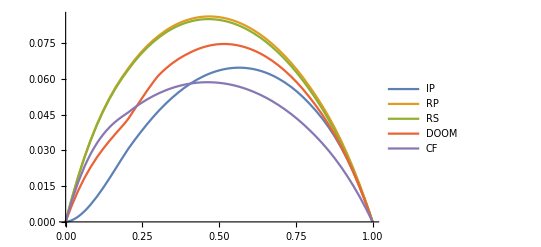

```mathematica
Plot[{costIP[x],costRP[x],costRS[x],costdoom[x], costCF[x]},{x,0,1},PlotLegends->{"IP","RP","RS","DOOM", "CF"}]
```

```mathematica
FindMaximum[costRP[x],{x,0.6}]
```

{0.0862143,{x→0.467719}}

```mathematica
FindMaximum[costRS[x],{x,0.6}]
```

{0.0850974,{x→0.465127}}

```mathematica
FindMaximum[costIP[x],{x,0.5}]
```

{0.0647138,{x→0.564994}}

```mathematica
FindMaximum[costdoom[x],{x,0.4}]
```

{0.0796886,{x→0.492504}}

```mathematica
FindMaximum[costCF[x],{x,0.3}]
```

{0.0586137,{x→0.462105}}

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
Plot[{costIP[x],costRP[x],costRS[x],costdoom[x],costCF[x]},{x,0,1},
PlotLegends->Placed[LineLegend[{"Upper Bound on Interleaved Prange","Upper Bound  on Random Prange","Upper Bound on Random Stern","Upper Bound DOOM", "CF"},LegendFunction->Framed,LabelStyle->20],{Center,Above}],
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{Style[displayLaTeX["e(R,q)"],FontSize->14,FontColor->Black],None},{Style[displayLaTeX["R"],FontSize->14,FontColor->Black],None}},
FrameTicks->All,
AspectRatio->1/2,
TicksStyle->Directive[FontSize,12],
ImageSize->800,
PlotRange->{{0,1.05},{0,0.09}}]
```

-Graphics-

```mathematica
directRP:={{0.1,0.0391369286742317},{0.2,0.0607694824452584},{0.3,0.0729650309708858},{0.4,0.0781079032671114},{0.5,0.0773474838721205},{0.6,0.0713034234756800},{0.7,0.0602952167255557},{0.8,0.0444426487163092},{0.9,0.0237883453171419
}};
PrependTo[directRP,{0,0}];
AppendTo[directRP,{1,0}];
costdirectRP:=Interpolation[directRP];
```

```mathematica
directIP:={{0.1,0.0219765397682611},{0.2,0.0450852090166716},{0.3,0.0594177041258281},{0.4,0.0667344218693606},{0.5,0.0681571213722178},{0.6,0.0642489622128572},{0.7,0.0552438185279594},{0.8,0.0413124507311077},{0.9,0.0224724601362694

}};
PrependTo[directIP,{0,0}];
AppendTo[directIP,{1,0}];
costdirectIP:=Interpolation[directIP];
```

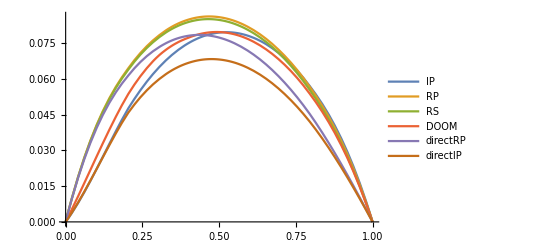

```mathematica
Plot[{costIP[x],costRP[x],costRS[x],costdoom[x],costdirectRP[x],costdirectIP[x]},{x,0,1},PlotLegends->{"IP","RP","RS","DOOM", "directRP","directIP"}]
```

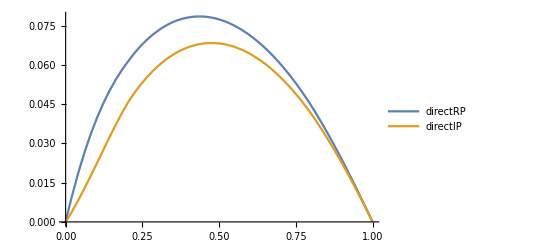

```mathematica
Plot[{costdirectRP[x],costdirectIP[x]},{x,0,1},PlotLegends->{"directRP","directIP"}]
```

```mathematica
FindMaximum[costdirectRP[x],{x,0.6}]
```

{0.0784819,{x→0.436051}}

```mathematica
FindMaximum[costdirectIP[x],{x,0.6}]
```

{0.0683232,{x→0.475251}}

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
Plot[{costdirectIP[x],costdirectRP[x]},{x,0,1},
PlotLegends->Placed[LineLegend[{"Simulated Interleaved Prange","Simulated Random Prange"},LegendFunction->Framed,LabelStyle->20],{Center,Above}],
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{Style[displayLaTeX["e(R,q)"],FontSize->14,FontColor->Black],None},{Style[displayLaTeX["R"],FontSize->14,FontColor->Black],None}},
FrameTicks->All,
AspectRatio->1/2,
TicksStyle->Directive[FontSize,12],
ImageSize->800,
PlotRange->{{0,1.05},{0,0.09}}]
```

-Graphics-